```mathematica
tests={1/Sqrt[3],-1/Sqrt[3]};
```

```mathematica
sinFunc[k_]:=Sin[(j+1)*Arg[I-k]]/(Sqrt[1+k^2]^(j+1))
```

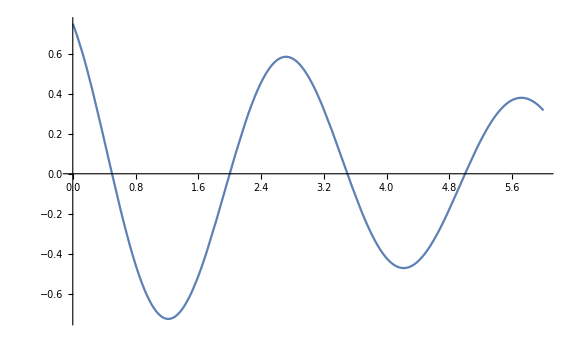
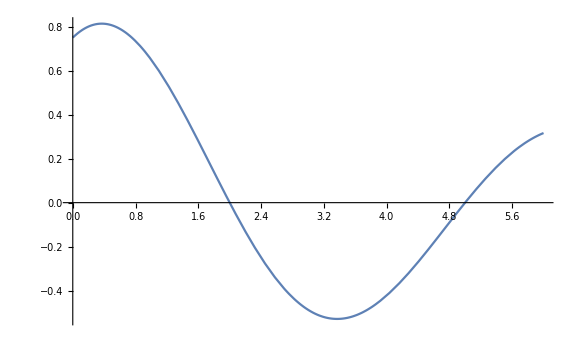
1/(√3) | -Graphics-
-1/(√3) | -Graphics-

```mathematica
Grid[Transpose[{tests,Table[Plot[i,{j,0,6},PlotRange->All,ImageSize->Large],{i,sinFunc[tests]}]}],Frame->All]
```

```mathematica
Rasterize[%]
```

-Graphics-